```mathematica
ClearAll[groundTruth,m,b];
groundTruth={m,b}={0.5,-1./3.};
```

```mathematica
ClearAll[nData,min,max];
nData=119;min=-1.;max=3.;
ClearAll[partials];
partials=Array[{#,1.0}&,nData,{min,max}];
```

```mathematica
ClearAll[fake];
fake[n_,σ_,A_,{m_,b_}]:=
Table[RandomVariate[NormalDistribution[0,σ]]+A⟦i⟧.{m,b},{i,n}];
```

```mathematica
ClearAll[data,noiseσ];
noiseσ=0.65;
data=fake[nData,noiseσ,partials,groundTruth];
```

```mathematica
ClearAll[model];
model=LinearModelFit[{partials⟦All,1⟧,data}ᵀ,x,x];
Normal[model]
```

-0.452862+0.43406 x

```mathematica
(*Association[(#->model[#])&/@model["Properties"]]*)
```

```mathematica
model["CovarianceMatrix"]//MatrixForm
```

(0.00532759 | -0.00226135
-0.00226135 | 0.00226135)

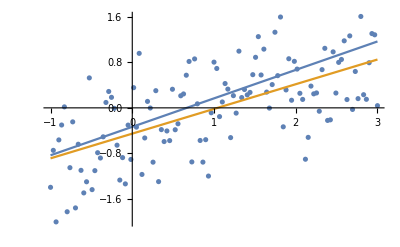

```mathematica
Show[ListPlot[{partials⟦All,1⟧,data}ᵀ],
Plot[{m x+b,model[x]},{x,min,max}]]
```

```mathematica
ClearAll[update];
update[{ξ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{LinearSolve[Π,(aᵀ.ζ+Λ.ξ)],Π}];

MatrixForm/@({({{mBar}, {bBar}}),Π}=
Fold[update,{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@data,List/@partials}ᵀ])
```

{(0.43406
-0.452862),(280.356 | 119.
119. | 119.)}

```mathematica
{xs,zs}={Table[partials⟦i,1⟧,{i,nData}],Table[model[partials⟦i,1⟧],{i,nData}]};
```

```mathematica
sdv=StandardDeviation[zs-data]
```

0.60149

```mathematica
1/sdv^2
```

2.76403

```mathematica
With[{basisFn=Function[i,List/@Reverse[partials⟦i⟧]]},
basisFn[42].basisFn[42]ᵀ]//MatrixForm
```

(1. | 0.389831
0.389831 | 0.151968)

```mathematica
(Ssum=With[{basisFn=Function[i,List/@Reverse[partials⟦i⟧]]},
Sum[basisFn[i].basisFn[i]ᵀ,{i,nData}]])//MatrixForm
```

(119. | 119.
119. | 280.356)

```mathematica
"Covariance of the Parameters"==(With[{α=0.005},α^-1 IdentityMatrix[2]]//MatrixForm)
```

Covariance of the Parameters==(200. | 0.
0. | 200.)

S  =  Inverse(α I_(Μ+1)+β∑_(n=1)^N ϕ (x_n)·ϕ (x_n)ᵀ)

```mathematica
ClearAll[S];
S[α_,β_]:=Inverse[α IdentityMatrix[2]+β Ssum]
```

```mathematica
ClearAll[s2,mmap];
With[{ϕ=Function[x,{{1},{x}}]},
s2[x_,α_,β_]:=β^-1+ϕ[x]ᵀ.S[α,β].ϕ[x];
mmap[x_,α_,β_]:=β ϕ[x]ᵀ.S[α,β].Sum[ϕ[xs⟦i⟧]zs⟦i⟧,{i,nData}]];
```

```mathematica
DynamicModule[{bishop=True},
Manipulate[
Module[{α,β},
α=If[bishop,10.^(-2logσw),10.^(2logσt)];
β=If[bishop,10.^(-2logσt),10.^(2logσw)];
Show[
ListPlot[{partials⟦All,1⟧,data}ᵀ],
Plot[{
m x+b,
model[x],
mmap[x,α,β]},
{x,min,max}],Frame->True,FrameLabel->{{"t",""},{"x",
Grid[{{"α: ",α,"        β: ",β}}]
}}]],
Column[{
SetterBar[Dynamic[bishop],{True->"α = 1/σ_w^2, β = 1/σ_t^2",False->"α = σ_t^2, β = σ_w^2"}],
Button["RESET",(logσw=-1.15;logσt=Log10[sdv])&],
Control[{{logσw,-1.15,"log_10 σ_w"},-2,1,Appearance->"Labeled"}],
Control[{{logσt,Log10[sdv],"log_10 σ_t"},-4,4,Appearance->"Labeled"}]}]]]
```

```mathematica
e1=(mmap[x,α,β]//FullSimplify)⟦1,1⟧
```

(β ((-0.000116523+0.00353104 x) α+(-0.452862+0.43406 x) β))/(0.0000520797 α^2+0.0207983 α β+1. β^2)

```mathematica
e2=(mmap[x,1/β,1/α]//FullSimplify)⟦1,1⟧
```

(β ((-2.23739+67.8008 x) α+(-8695.56+8334.54 x) β))/(α^2+399.356 α β+19201.4 β^2)

```mathematica
(e1-e2)//FullSimplify
```

0.

```mathematica
Manipulate[Column[{
mmap[x,α,β],
mmap[x,1/β,1/α],
mmap[x,α,β]//FullSimplify,
mmap[x,1/β,1/α]//FullSimplify
}],
{{α,0.005},0,1000},
{{β,1/0.03},0,1000}]
```

```mathematica
ClearAll[x,z,S,SD,Ssum,SMap,SDmap];
Ssum[Μ_,Ν_]:=
With[{ϕ=Function[n,Table[{Subscript[x, n]^j},{j,0,Μ}]]},
Sum[ϕ[n].ϕ[n]ᵀ,{n,Ν}]];
SD[Μ_,Ν_,α_,β_]:=
With[{m=α IdentityMatrix[Μ+1]+β Ssum[Μ,Ν]},
Det[m]Inverse[m]//FullSimplify];
SDmap[Μ_,Ν_,α_,β_]:=
With[{
ϕ=Function[n,Table[{Subscript[x, n]^j},{j,0,Μ}]],
ϕx=Table[{x^j},{j,0,Μ}]},
β ϕxᵀ.SD[Μ,Ν,α,β].Sum[ϕ[n] Subscript[z, n],{n,Ν}]];
SMap[Μ_,Ν_,α_,β_]:=
SDmap[Μ,Ν,α,β]/Det[α IdentityMatrix[Μ+1]+β Ssum[Μ,Ν]];
(*SMap[2,3,α,β]//FullSimplify
SMap[2,3,1/β,1/α]//FullSimplify*)
(SMap[2,3,α,β]-SMap[2,3,1/β,1/α])//FullSimplify
(*SD[2,3,α,β]*)
```

{{0}}

```mathematica
(SMap[3,4,α,β]-SMap[3,4,1/β,1/α])//Simplify
```

{{0}}

(α=σ_ζ^2 | β=σ_ξ^2
α=1/σ_ξ^2 | β=1/σ_ζ^2)